# Интерполационен полином на Лагранж

Задача: (a и b са съответно предпоследната и последната цифра на факултетния номер)
1. Да се състави таблица (x_i, f(x_i)), където
x_i = -a + i(0.2), i = OverBar[0,10]         f(x) = ln(x^2 + b + 1)
2. Изберете 3 подходящи точки, по които да се построи интерполационен полином за изчисляване на приближената стойност на функцията в точката
z = -a + (0.23)b + 0.02
3. Изберете 4 подходящи точки, по които да се построи интерполационен полином за изчисляване на приближената стойност на функцията в същата точка.
4. Да се построят интерполационните полиноми на Лагранж по избраните възли (отделно за подточка 2 и за подточка 3).
5. Да се пресметнат приближените стойности на функцията в дадената точка (отделно за подточка 2 и за подточка 3).
6. Да се оцени грешката на полученото приближение (отделно за подточка 2 и за подточка 3).
7. Да се сравнят резултатите от двете намерени приближени стойности.

## 1. Съставяне на таблицата

```mathematica
xt = Table[-6+i*0.2,{i,0,10}]
```

{-6.,-5.8,-5.6,-5.4,-5.2,-5.,-4.8,-4.6,-4.4,-4.2,-4.}

```mathematica
f[x_]:=Log[x^2 + 8]
yt = f[xt]
```

{3.78419,3.72906,3.67275,3.61523,3.55649,3.49651,3.43528,3.3728,3.30908,3.24415,3.17805}

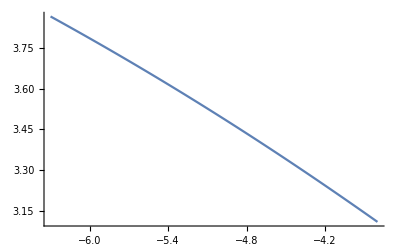

```mathematica
grf = Plot[f[x],{x,-6.3,-3.8}]
```

```mathematica
n =Length[xt]
points = Table[{xt[[i]],yt[[i]]},{i,1,n}]
```

11

{{-6.,3.78419},{-5.8,3.72906},{-5.6,3.67275},{-5.4,3.61523},{-5.2,3.55649},{-5.,3.49651},{-4.8,3.43528},{-4.6,3.3728},{-4.4,3.30908},{-4.2,3.24415},{-4.,3.17805}}

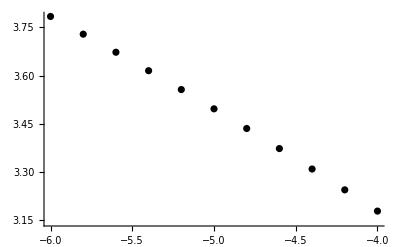

```mathematica
grp = ListPlot[points, PlotStyle->Black]
```

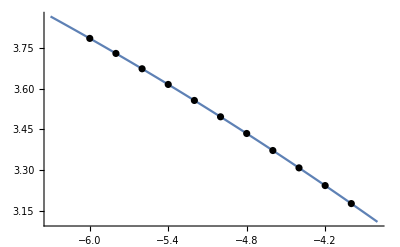

```mathematica
Show[grf, grp]
```

## 2. Избираме 3 точки за z = -a + (0.23)b + 0.02 (квадратична интерполация)

```mathematica
z = -6 + (0.23 * 7) + 0.02
```

-4.37

```mathematica
L1[x_]:= 3.3728*((x+4.4)(x+4.2))/((-4.6+4.4)(-4.6+4.2)) +3.30908*((x+4.6)(x + 4.2))/((-4.4+4.6)(-4.4 + 4.2))+3.24415*((x+ 4.6)(x + 4.4))/((-4.2+ 4.6)(-4.2 + 4.4))
```

```mathematica
Expand[L1[x]]
```

1.60111-0.454725 x-0.015125 x^2

### Проверка на интерполационните условия

```mathematica
L1[-4.6]
L1[-4.4]
L1[-4.2]
```

3.3728

3.30908

3.24415

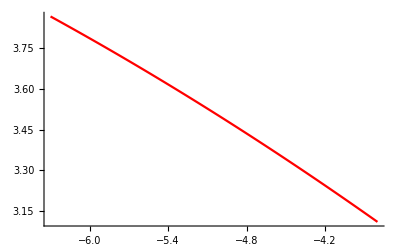

```mathematica
grL1 = Plot[L1[x],{x,-6.3,-3.8}, PlotStyle->Red]
```

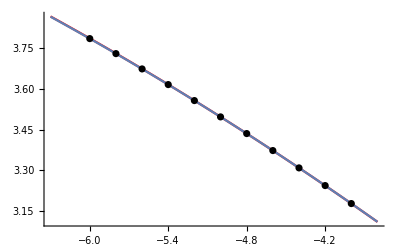

```mathematica
Show[grL1, grf,grp]
```

### Пресмятане на приближена стойност

```mathematica
L1[-4.37]
```

3.29942

за сравнение с истинската стойност

```mathematica
f[-4.37]
```

3.29942

### Оценка на грешката

#### Теоретична грешка

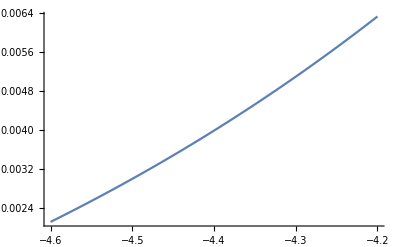

```mathematica
Plot[Abs[f'''[x]],{x,-4.6,-4.2}]
```

```mathematica
M2 = Abs[f'''[-4.2]]
```

0.00633888

```mathematica
R1[x_]:=M2/(3!)Abs[(x+4.6)(x+4.4)(x+4.2)]
```

```mathematica
R1[-4.37]
```

1.23925×10^-6

#### Истинска грешка

```mathematica
Abs[L1[-4.37]-f[-4.37]]
```

1.6927×10^-6

## 2. Избираме 4 точки за z = -a + (0.23)b + 0.02 (кубична интерполация)

```mathematica
L2[x_]:= 3.3728*((x+4.4)(x+ 4.2)(x+4))/((-4.6+4.4)(-4.6+ 4.2)(-4.6+4))  +3.30908*((x+4.6)(x+ 4.2)(x+4))/((-4.4+4.6)(-4.4+ 4.2)(-4.4+4))+3.24415*((x+4.6)(x+ 4.4)(x+4))/((-4.2+4.6)(-4.2+ 4.4)(-4.2+4)) + 3.17805 * ((x+4.6)(x+ 4.4)(x+4.2))/((-4+4.6)(-4+ 4.4)(-4+4.2))
```

```mathematica
Expand[L2[x]]
```

1.67195-0.406358 x-0.004125 x^2+0.000833333 x^3

### Проверка на интерполационните условия

```mathematica
L2[-4.6]
L2[-4.4]
L2[-4.2]
L2[-4]
```

3.3728

3.30908

3.24415

3.17805

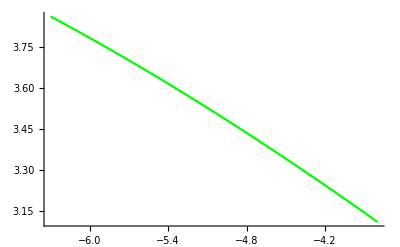

```mathematica
grL2 = Plot[L2[x],{x,-6.3,-3.8}, PlotStyle->Green]
```

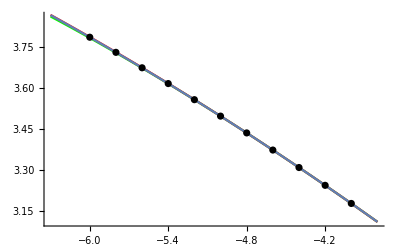

```mathematica
Show[grL2,grL1, grf,grp]
```

### Пресмятане на приближена стойност

```mathematica
L2[-4.37]
```

3.29942

за сравнение с истинската стойност

```mathematica
f[-4.37]
```

3.29942

### Оценка на грешката

#### Теоретична грешка

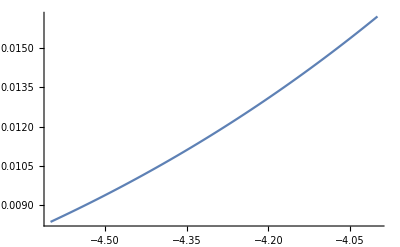

```mathematica
Plot[Abs[f''''[x]],{x,-4.6,-4}]
```

```mathematica
M3 = N[Abs[f''''[-4]]]
```

0.0162037

```mathematica
R2[x_]:=M3/(4!)Abs[(x+4.6)(x+4.4)(x+4.2)(x+4)]
```

```mathematica
R2[-4.37]
```

2.93024×10^-7

#### Истинска грешка

```mathematica
Abs[L2[-4.37]-f[-4.37]]
```

2.6702×10^-6